# The adiabatic Theorem of a TLS

```mathematica
$Assumptions={g∈ Reals,ω∈ Reals}
```

{g∈ℝ,ω∈ℝ}

## Two TLS’s

#### Definitions

```mathematica
DirectProduct[M1_,M2_]:=ArrayFlatten[Outer[Times,M1,M2]]
Kron[V1_,V2_]:=Flatten[Outer[Times,V1,V2]]
KetBra[V1_,V2_]:=Outer[Times,V1,Conjugate[V2]]
L1=2;L2=1;(* The angular momentum *)
X=IdentityMatrix[2*L1+1]*0;Y=X;Z=X; (* Definitions of X,Y,Z *)
For[m=1,m≤2*L1+1,m++,Z[[m,m]]=m-L1-1];
For[m=1,m<2*L1+1,m++,X[[m,m+1]]=Sqrt[(1+2 L1-m) m];X[[m+1,m]]=Sqrt[(1+2 L1-m) m]];
For[m=1,m<2*L1+1,m++,Y[[m,m+1]]=-I*Sqrt[(1+2 L1-m) m];Y[[m+1,m]]=I*Sqrt[(1+2 L1-m) m]];Clear[m];
X=X/2;
Y=Y/2;
Z=Z;
Sp=X+I Y;
Sm=X-I Y;
x=IdentityMatrix[2*L2+1]*0;y=x;z=x; (* Definitions of X,Y,Z *)
For[m=1,m≤2*L2+1,m++,z[[m,m]]=m-L2-1];
For[m=1,m<2*L2+1,m++,x[[m,m+1]]=Sqrt[(1+2 L2-m) m];x[[m+1,m]]=Sqrt[(1+2 L2-m) m]];
For[m=1,m<2*L2+1,m++,y[[m,m+1]]=-I*Sqrt[(1+2 L2-m) m];y[[m+1,m]]=I*Sqrt[(1+2 L2-m) m]];
x=x/2;
y=y/2;
z=z;
sp=x+I y;
sm=x-I y;
X1=DirectProduct[X,IdentityMatrix[2 L2+1]];
Y1=DirectProduct[Y,IdentityMatrix[2 L2 +1]];
Z1=DirectProduct[Z,IdentityMatrix[2 L2 +1]];
X2=DirectProduct[IdentityMatrix[2 L1+1],x];
Y2=DirectProduct[IdentityMatrix[2 L1 +1],y];
Z2=DirectProduct[IdentityMatrix[2 L1 +1],z];
```

#### Hamiltonian

```mathematica
g=0;ω=1;Clear[δl];
ham=ω Z1 + ω Z2 + g Z1.Z2;(* Definition of Hamiltonian *)
MatrixForm[ham]
```

(-3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

#### Dynamics

(-3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

{-3 v_1[t]==ⅈ v_1'[t],-2 v_2[t]==ⅈ v_2'[t],-v_3[t]==ⅈ v_3'[t],-2 v_4[t]==ⅈ v_4'[t],-v_5[t]==ⅈ v_5'[t],0==ⅈ v_6'[t],-v_7[t]==ⅈ v_7'[t],0==ⅈ v_8'[t],v_9[t]==ⅈ v_9'[t],0==ⅈ v_10'[t],v_11[t]==ⅈ v_11'[t],2 v_12[t]==ⅈ v_12'[t],v_13[t]==ⅈ v_13'[t],2 v_14[t]==ⅈ v_14'[t],3 v_15[t]==ⅈ v_15'[t]}

{1/4,0,0,0,0,-1/2,0,0,0,0,(√(3/2))/2,0,0,0,0,-1/2,0,0,0,0,1/4,0,0,0,0}

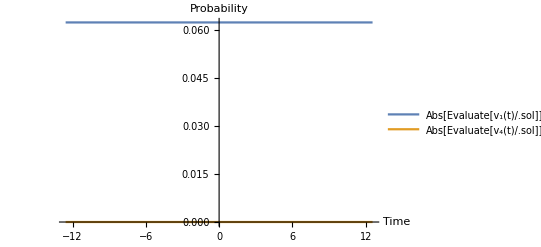

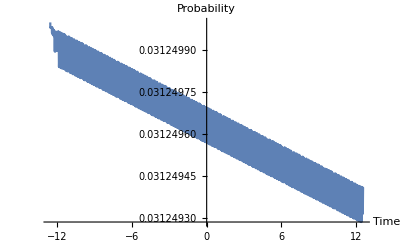

```mathematica
Tot=2 π 2;
ham1=ham;
MatrixForm[ham]
Vec=Vec=Table[Subscript[v, i][t],{i,1,(2L1+1)(2L2+1)}];
eqs = Table[(ham1.Vec)[[k]]==I D[Vec[[k]],t],{k,1,(2L1+1)(2L2+1)}]
va=Normalize[Eigenvectors[X][[1]]];vb=Normalize[Eigenvectors[Z][[1]]];vecini=Kron[va,vb]
initial=Table[Subscript[v, i][-Tot]==vecini[[i]],{i,1,(2L1+1)(2L2+1)}];
sol=NDSolve[Join[eqs,initial],Vec,{t,-Tot,Tot},MaxSteps->10^7];
Plot[{Abs[Evaluate[Subscript[v, 1][t]/.sol]]^2,Abs[Evaluate[Subscript[v, 4][t]/.sol]]^2},{t,-Tot,Tot},PlotRange-> All,AxesLabel->{Time,Probability},PlotLegends->"Expressions"]
Plot[1/2 Abs[(Evaluate[Subscript[v, 1][t]/.sol][[1]])+(Evaluate[Subscript[v, 3][t]/.sol][[1]])I]^2,{t,-Tot,Tot},PlotRange-> All,AxesLabel->{Time,Probability}]
```

#### Density Matrix

```mathematica
ρ=KetBra[Vec,Vec];
MatrixForm[ρ]
mat11=DirectProduct[KetBra[{0,1},{0,1}],IdentityMatrix[2]];
mat22=DirectProduct[KetBra[{1,0},{1,0}],IdentityMatrix[2]];
mat21=DirectProduct[KetBra[{1,0},{0,1}],IdentityMatrix[2]];
mat12=DirectProduct[KetBra[{0,1},{1,0}],IdentityMatrix[2]];
ρ11=Tr[ρ.mat11];
ρ12=Tr[ρ.mat12];
ρ21=Tr[ρ.mat21];
ρ22=Tr[ρ.mat22];
ρ1={{ρ11,ρ12},{ρ21,ρ22}};
MatrixForm[ρ1]
ρ1A=(ρ1/.sol)[[1]]

mat11B=DirectProduct[IdentityMatrix[2],KetBra[{0,1},{0,1}]];
mat22B=DirectProduct[IdentityMatrix[2],KetBra[{1,0},{1,0}]];
mat21B=DirectProduct[IdentityMatrix[2],KetBra[{1,0},{0,1}]];
mat12B=DirectProduct[IdentityMatrix[2],KetBra[{0,1},{1,0}]];
ρ11B=Tr[ρ.mat11B];
ρ12B=Tr[ρ.mat12B];
ρ21B=Tr[ρ.mat21B];
ρ22B=Tr[ρ.mat22B];
ρ1B={{ρ11B,ρ12B},{ρ21B,ρ22B}};
MatrixForm[ρ1B]
ρ1BB=(ρ1B/.sol)[[1]];
```

(Conjugate[v_1[t]] v_1[t] | Conjugate[v_2[t]] v_1[t] | Conjugate[v_3[t]] v_1[t] | Conjugate[v_4[t]] v_1[t] | Conjugate[v_5[t]] v_1[t] | Conjugate[v_6[t]] v_1[t] | Conjugate[v_7[t]] v_1[t] | Conjugate[v_8[t]] v_1[t] | Conjugate[v_9[t]] v_1[t] | Conjugate[v_10[t]] v_1[t] | Conjugate[v_11[t]] v_1[t] | Conjugate[v_12[t]] v_1[t] | Conjugate[v_13[t]] v_1[t] | Conjugate[v_14[t]] v_1[t] | Conjugate[v_15[t]] v_1[t]
Conjugate[v_1[t]] v_2[t] | Conjugate[v_2[t]] v_2[t] | Conjugate[v_3[t]] v_2[t] | Conjugate[v_4[t]] v_2[t] | Conjugate[v_5[t]] v_2[t] | Conjugate[v_6[t]] v_2[t] | Conjugate[v_7[t]] v_2[t] | Conjugate[v_8[t]] v_2[t] | Conjugate[v_9[t]] v_2[t] | Conjugate[v_10[t]] v_2[t] | Conjugate[v_11[t]] v_2[t] | Conjugate[v_12[t]] v_2[t] | Conjugate[v_13[t]] v_2[t] | Conjugate[v_14[t]] v_2[t] | Conjugate[v_15[t]] v_2[t]
Conjugate[v_1[t]] v_3[t] | Conjugate[v_2[t]] v_3[t] | Conjugate[v_3[t]] v_3[t] | Conjugate[v_4[t]] v_3[t] | Conjugate[v_5[t]] v_3[t] | Conjugate[v_6[t]] v_3[t] | Conjugate[v_7[t]] v_3[t] | Conjugate[v_8[t]] v_3[t] | Conjugate[v_9[t]] v_3[t] | Conjugate[v_10[t]] v_3[t] | Conjugate[v_11[t]] v_3[t] | Conjugate[v_12[t]] v_3[t] | Conjugate[v_13[t]] v_3[t] | Conjugate[v_14[t]] v_3[t] | Conjugate[v_15[t]] v_3[t]
Conjugate[v_1[t]] v_4[t] | Conjugate[v_2[t]] v_4[t] | Conjugate[v_3[t]] v_4[t] | Conjugate[v_4[t]] v_4[t] | Conjugate[v_5[t]] v_4[t] | Conjugate[v_6[t]] v_4[t] | Conjugate[v_7[t]] v_4[t] | Conjugate[v_8[t]] v_4[t] | Conjugate[v_9[t]] v_4[t] | Conjugate[v_10[t]] v_4[t] | Conjugate[v_11[t]] v_4[t] | Conjugate[v_12[t]] v_4[t] | Conjugate[v_13[t]] v_4[t] | Conjugate[v_14[t]] v_4[t] | Conjugate[v_15[t]] v_4[t]
Conjugate[v_1[t]] v_5[t] | Conjugate[v_2[t]] v_5[t] | Conjugate[v_3[t]] v_5[t] | Conjugate[v_4[t]] v_5[t] | Conjugate[v_5[t]] v_5[t] | Conjugate[v_6[t]] v_5[t] | Conjugate[v_7[t]] v_5[t] | Conjugate[v_8[t]] v_5[t] | Conjugate[v_9[t]] v_5[t] | Conjugate[v_10[t]] v_5[t] | Conjugate[v_11[t]] v_5[t] | Conjugate[v_12[t]] v_5[t] | Conjugate[v_13[t]] v_5[t] | Conjugate[v_14[t]] v_5[t] | Conjugate[v_15[t]] v_5[t]
Conjugate[v_1[t]] v_6[t] | Conjugate[v_2[t]] v_6[t] | Conjugate[v_3[t]] v_6[t] | Conjugate[v_4[t]] v_6[t] | Conjugate[v_5[t]] v_6[t] | Conjugate[v_6[t]] v_6[t] | Conjugate[v_7[t]] v_6[t] | Conjugate[v_8[t]] v_6[t] | Conjugate[v_9[t]] v_6[t] | Conjugate[v_10[t]] v_6[t] | Conjugate[v_11[t]] v_6[t] | Conjugate[v_12[t]] v_6[t] | Conjugate[v_13[t]] v_6[t] | Conjugate[v_14[t]] v_6[t] | Conjugate[v_15[t]] v_6[t]
Conjugate[v_1[t]] v_7[t] | Conjugate[v_2[t]] v_7[t] | Conjugate[v_3[t]] v_7[t] | Conjugate[v_4[t]] v_7[t] | Conjugate[v_5[t]] v_7[t] | Conjugate[v_6[t]] v_7[t] | Conjugate[v_7[t]] v_7[t] | Conjugate[v_8[t]] v_7[t] | Conjugate[v_9[t]] v_7[t] | Conjugate[v_10[t]] v_7[t] | Conjugate[v_11[t]] v_7[t] | Conjugate[v_12[t]] v_7[t] | Conjugate[v_13[t]] v_7[t] | Conjugate[v_14[t]] v_7[t] | Conjugate[v_15[t]] v_7[t]
Conjugate[v_1[t]] v_8[t] | Conjugate[v_2[t]] v_8[t] | Conjugate[v_3[t]] v_8[t] | Conjugate[v_4[t]] v_8[t] | Conjugate[v_5[t]] v_8[t] | Conjugate[v_6[t]] v_8[t] | Conjugate[v_7[t]] v_8[t] | Conjugate[v_8[t]] v_8[t] | Conjugate[v_9[t]] v_8[t] | Conjugate[v_10[t]] v_8[t] | Conjugate[v_11[t]] v_8[t] | Conjugate[v_12[t]] v_8[t] | Conjugate[v_13[t]] v_8[t] | Conjugate[v_14[t]] v_8[t] | Conjugate[v_15[t]] v_8[t]
Conjugate[v_1[t]] v_9[t] | Conjugate[v_2[t]] v_9[t] | Conjugate[v_3[t]] v_9[t] | Conjugate[v_4[t]] v_9[t] | Conjugate[v_5[t]] v_9[t] | Conjugate[v_6[t]] v_9[t] | Conjugate[v_7[t]] v_9[t] | Conjugate[v_8[t]] v_9[t] | Conjugate[v_9[t]] v_9[t] | Conjugate[v_10[t]] v_9[t] | Conjugate[v_11[t]] v_9[t] | Conjugate[v_12[t]] v_9[t] | Conjugate[v_13[t]] v_9[t] | Conjugate[v_14[t]] v_9[t] | Conjugate[v_15[t]] v_9[t]
Conjugate[v_1[t]] v_10[t] | Conjugate[v_2[t]] v_10[t] | Conjugate[v_3[t]] v_10[t] | Conjugate[v_4[t]] v_10[t] | Conjugate[v_5[t]] v_10[t] | Conjugate[v_6[t]] v_10[t] | Conjugate[v_7[t]] v_10[t] | Conjugate[v_8[t]] v_10[t] | Conjugate[v_9[t]] v_10[t] | Conjugate[v_10[t]] v_10[t] | Conjugate[v_11[t]] v_10[t] | Conjugate[v_12[t]] v_10[t] | Conjugate[v_13[t]] v_10[t] | Conjugate[v_14[t]] v_10[t] | Conjugate[v_15[t]] v_10[t]
Conjugate[v_1[t]] v_11[t] | Conjugate[v_2[t]] v_11[t] | Conjugate[v_3[t]] v_11[t] | Conjugate[v_4[t]] v_11[t] | Conjugate[v_5[t]] v_11[t] | Conjugate[v_6[t]] v_11[t] | Conjugate[v_7[t]] v_11[t] | Conjugate[v_8[t]] v_11[t] | Conjugate[v_9[t]] v_11[t] | Conjugate[v_10[t]] v_11[t] | Conjugate[v_11[t]] v_11[t] | Conjugate[v_12[t]] v_11[t] | Conjugate[v_13[t]] v_11[t] | Conjugate[v_14[t]] v_11[t] | Conjugate[v_15[t]] v_11[t]
Conjugate[v_1[t]] v_12[t] | Conjugate[v_2[t]] v_12[t] | Conjugate[v_3[t]] v_12[t] | Conjugate[v_4[t]] v_12[t] | Conjugate[v_5[t]] v_12[t] | Conjugate[v_6[t]] v_12[t] | Conjugate[v_7[t]] v_12[t] | Conjugate[v_8[t]] v_12[t] | Conjugate[v_9[t]] v_12[t] | Conjugate[v_10[t]] v_12[t] | Conjugate[v_11[t]] v_12[t] | Conjugate[v_12[t]] v_12[t] | Conjugate[v_13[t]] v_12[t] | Conjugate[v_14[t]] v_12[t] | Conjugate[v_15[t]] v_12[t]
Conjugate[v_1[t]] v_13[t] | Conjugate[v_2[t]] v_13[t] | Conjugate[v_3[t]] v_13[t] | Conjugate[v_4[t]] v_13[t] | Conjugate[v_5[t]] v_13[t] | Conjugate[v_6[t]] v_13[t] | Conjugate[v_7[t]] v_13[t] | Conjugate[v_8[t]] v_13[t] | Conjugate[v_9[t]] v_13[t] | Conjugate[v_10[t]] v_13[t] | Conjugate[v_11[t]] v_13[t] | Conjugate[v_12[t]] v_13[t] | Conjugate[v_13[t]] v_13[t] | Conjugate[v_14[t]] v_13[t] | Conjugate[v_15[t]] v_13[t]
Conjugate[v_1[t]] v_14[t] | Conjugate[v_2[t]] v_14[t] | Conjugate[v_3[t]] v_14[t] | Conjugate[v_4[t]] v_14[t] | Conjugate[v_5[t]] v_14[t] | Conjugate[v_6[t]] v_14[t] | Conjugate[v_7[t]] v_14[t] | Conjugate[v_8[t]] v_14[t] | Conjugate[v_9[t]] v_14[t] | Conjugate[v_10[t]] v_14[t] | Conjugate[v_11[t]] v_14[t] | Conjugate[v_12[t]] v_14[t] | Conjugate[v_13[t]] v_14[t] | Conjugate[v_14[t]] v_14[t] | Conjugate[v_15[t]] v_14[t]
Conjugate[v_1[t]] v_15[t] | Conjugate[v_2[t]] v_15[t] | Conjugate[v_3[t]] v_15[t] | Conjugate[v_4[t]] v_15[t] | Conjugate[v_5[t]] v_15[t] | Conjugate[v_6[t]] v_15[t] | Conjugate[v_7[t]] v_15[t] | Conjugate[v_8[t]] v_15[t] | Conjugate[v_9[t]] v_15[t] | Conjugate[v_10[t]] v_15[t] | Conjugate[v_11[t]] v_15[t] | Conjugate[v_12[t]] v_15[t] | Conjugate[v_13[t]] v_15[t] | Conjugate[v_14[t]] v_15[t] | Conjugate[v_15[t]] v_15[t])

Dot::dotsh: Tensors … and {{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}} have incompatible shapes.

Dot::dotsh: Tensors … and {{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}} have incompatible shapes.

Dot::dotsh: Tensors … and {{0,0,1,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}} have incompatible shapes.

Dot::dotsh: Tensors … and {{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}} have incompatible shapes.

(1)
 |  |  |  |

Dot::dotsh: Tensors {{«1»},{«1»},{«1»},{«1»},{«1»},«5»,{Conjugate[«1»] «1»[t],«13»,Conjugate[«1»] «1»},{Conjugate[«1»] «1»[t],Conjugate[«1»] «1»,Conjugate[«1»] «1»[t],«10»,Conjugate[InterpolatingFunction[{{-12.5664,12.5664}},«3»,{Automatic}][t]] «1»,Conjugate[«1»] «1»},{«1»},{Conjugate[«1»] «1»,«14»},{«1»}} and {{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}} have incompatible shapes.

Dot::dotsh: Tensors {{«1»},{«1»},{«1»},{«1»},{«1»},«5»,{Conjugate[«1»] «1»[t],«13»,Conjugate[«1»] «1»},{Conjugate[«1»] «1»[t],Conjugate[«1»] «1»,Conjugate[«1»] «1»[t],«10»,Conjugate[InterpolatingFunction[{{-12.5664,12.5664}},«3»,{Automatic}][t]] «1»,Conjugate[«1»] «1»},{«1»},{Conjugate[«1»] «1»,«14»},{«1»}} and {{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}} have incompatible shapes.

Dot::dotsh: Tensors {{«1»},{«1»},{«1»},{«1»},{«1»},«5»,{Conjugate[«1»] «1»[t],«13»,Conjugate[«1»] «1»},{Conjugate[«1»] «1»[t],Conjugate[«1»] «1»,Conjugate[«1»] «1»[t],«10»,Conjugate[InterpolatingFunction[{{-12.5664,12.5664}},«3»,{Automatic}][t]] «1»,Conjugate[«1»] «1»},{«1»},{Conjugate[«1»] «1»,«14»},{«1»}} and {{0,0,1,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{{Tr[{{Conjugate[InterpolatingFunction[…][t]] InterpolatingFunction[…][t],Conjugate[InterpolatingFunction[…][t]] InterpolatingFunction[…][t],Conjugate[InterpolatingFunction[…][t]] InterpolatingFunction[…][t],Conjugate[InterpolatingFunction[…][t]] InterpolatingFunction[…][t],7,Conjugate[InterpolatingFunction[…][t]] InterpolatingFunction[…][t],Conjugate[InterpolatingFunction[…][t]] InterpolatingFunction[…][t],Conjugate[InterpolatingFunction[…][t]] InterpolatingFunction[…][t],Conjugate[InterpolatingFunction[…][t]] InterpolatingFunction[…][t]},13,{Conjugate[InterpolatingFunction[…][t]] 1[t],14}}.{1}],Tr[1]},{1}}
 |  |  |  |

Dot::dotsh: Tensors … and {{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,1}} have incompatible shapes.

Dot::dotsh: Tensors … and {{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,0,1,0}} have incompatible shapes.

Dot::dotsh: Tensors … and {{0,1,0,0},{0,0,0,0},{0,0,0,1},{0,0,0,0}} have incompatible shapes.

Dot::dotsh: Tensors … and {{1,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}} have incompatible shapes.

(1)
 |  |  |  |

Dot::dotsh: Tensors {{«1»},{«1»},{«1»},{«1»},{«1»},«5»,{Conjugate[«1»] «1»[t],«13»,Conjugate[«1»] «1»},{Conjugate[«1»] «1»[t],Conjugate[«1»] «1»,Conjugate[«1»] «1»[t],«10»,Conjugate[InterpolatingFunction[{{-12.5664,12.5664}},«3»,{Automatic}][t]] «1»,Conjugate[«1»] «1»},{«1»},{Conjugate[«1»] «1»,«14»},{«1»}} and {{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,1}} have incompatible shapes.

Dot::dotsh: Tensors {{«1»},{«1»},{«1»},{«1»},{«1»},«5»,{Conjugate[«1»] «1»[t],«13»,Conjugate[«1»] «1»},{Conjugate[«1»] «1»[t],Conjugate[«1»] «1»,Conjugate[«1»] «1»[t],«10»,Conjugate[InterpolatingFunction[{{-12.5664,12.5664}},«3»,{Automatic}][t]] «1»,Conjugate[«1»] «1»},{«1»},{Conjugate[«1»] «1»,«14»},{«1»}} and {{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,0,1,0}} have incompatible shapes.

Dot::dotsh: Tensors {{«1»},{«1»},{«1»},{«1»},{«1»},«5»,{Conjugate[«1»] «1»[t],«13»,Conjugate[«1»] «1»},{Conjugate[«1»] «1»[t],Conjugate[«1»] «1»,Conjugate[«1»] «1»[t],«10»,Conjugate[InterpolatingFunction[{{-12.5664,12.5664}},«3»,{Automatic}][t]] «1»,Conjugate[«1»] «1»},{«1»},{Conjugate[«1»] «1»,«14»},{«1»}} and {{0,1,0,0},{0,0,0,0},{0,0,0,1},{0,0,0,0}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
step=0.01;
tab=Table[ρ1A,{t,-Tot+step,Tot-step,step}];
Len1=Length[tab];
bloch1=Table[ρ=tab[[k]];
{Re[ρ[[1,2]]+ρ[[2,1]]],Re[I(ρ[[1,2]]-ρ[[2,1]])],Re[ρ[[1,1]]-ρ[[2,2]]]},{k,1,Len1}];
Times1=Table[t,{t,-Tot+step,Tot-step,step}];

tabB=Table[ρ1BB,{t,-Tot+step,Tot-step,step}];
bloch1B=Table[ρ=tabB[[k]];
{Re[ρ[[1,2]]+ρ[[2,1]]],Re[I(ρ[[1,2]]-ρ[[2,1]])],Re[ρ[[1,1]]-ρ[[2,2]]]},{k,1,Len1}];
```

Dot::dotsh: Tensors {{0.0625+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.124944-0.00374944 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.152971+0.00612209 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«12»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}} and {{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,1}} have incompatible shapes.

Dot::dotsh: Tensors {{0.0625+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.124944-0.00374944 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.152971+0.00612209 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«12»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}} and {{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}} have incompatible shapes.

Dot::dotsh: Tensors {{0.0625+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.124944-0.00374944 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.152971+0.00612209 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«12»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}} and {{0,0,1,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors {{0.0625+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.124944-0.00374944 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.152971+0.00612209 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«12»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}} and {{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,1}} have incompatible shapes.

Dot::dotsh: Tensors {{0.0625+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.124944-0.00374944 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.152971+0.00612209 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«12»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}} and {{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,0,1,0}} have incompatible shapes.

Dot::dotsh: Tensors {{0.0625+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.124944-0.00374944 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.152971+0.00612209 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«12»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}} and {{0,1,0,0},{0,0,0,0},{0,0,0,1},{0,0,0,0}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

#### Expectation Values

```mathematica
Vecsol=(Vec/.sol)[[1]];
```

```mathematica
ex1[t_]=Conjugate[Vecsol].X1.Vecsol;
ey1[t_]=Conjugate[Vecsol].Y1.Vecsol;
ez1[t_]=Conjugate[Vecsol].Z1.Vecsol;
ex2[t_]=Conjugate[Vecsol].X2.Vecsol;
ey2[t_]=Conjugate[Vecsol].Y2.Vecsol;
ez2[t_]=Conjugate[Vecsol].Z2.Vecsol;
```

```mathematica
bl[t_]={ex1[t],ey1[t],ez1[t]};
bl2[t_]={ex2[t],ey2[t],ez2[t]};
bl2[5]
```

{0.+0. ⅈ,0.+0. ⅈ,0.187501+0. ⅈ}

## Bloch sphere, Bloch vectors definitions - runs automatically

#### Colors, Bloch sphere, etc. definitions

```mathematica
plotDefinitions[xSimNameGraph_]:=(

green=RGBColor[0/255,172/255,75/255];
lgreen=RGBColor[119/255,255/255,178/255];
blue=RGBColor[0/255,103/255,153/255];
lblue=RGBColor[112/255,208/255,255/255];
red=RGBColor[242/255,130/255,0/255];
lred=RGBColor[255/255,205/255,147/255];

(* axes definition for the Bloch sphere *)
axes=
Graphics3D[{Black,Opacity[0.2],Specularity[1],Sphere[{0,0,0}],Opacity[1],
Arrowheads[.03],Arrow[{{0,-1.2,0},{0,1.2,0}}],
Arrow[{{0,0,-1.2},{0,0,1.2}}],
Arrow[{{-1.2,0,0},{1.2,0,0}}],Text[Style[Row[{Sphere}],24,Bold], {0,0,1.45}],
Text[Style[Row[{"ρ_22-ρ_11"}], 16,Bold], {0,0,1.25}],
Text[Style[Row[{"Im(ρ_12)"}], 16,Bold], {0,1.28,-0.1}],
Text[Style[Row[{"Re(ρ_12)"}], 16,Bold], {1.28,0,-0.1}]},Boxed->False];


(* the axes definition for video export is slightly different due to the ImageSize for export *)
axesVideo=
Graphics3D[{Black,Opacity[0.2],Specularity[1],Sphere[{0,0,0}],Opacity[1],
Arrowheads[.03],Arrow[{{0,-1.2,0},{0,1.2,0}}],
Arrow[{{0,0,-1.2},{0,0,1.2}}],
Arrow[{{-1.2,0,0},{1.2,0,0}}],Text[Style[Row[{xSimNameGraph}],8/5 24,Bold], {0,0,1.4}],
Text[Style[Row[{"ρ_22-ρ_11"}],8/5 16,Bold], {0,0,1.25}],
Text[Style[Row[{"Im(ρ_12)"}],8/5 16,Bold], {0,1.28,-0.1}],
Text[Style[Row[{"Re(ρ_12)"}],8/5 16,Bold], {1.28,0,-0.1}]},Boxed->False] (* Export[...,"VideoEncoding"->"Uncompressed",ImageSize->Large]*);

(* planes definitions for the Bloch sphere *)
sphaericLines=ParametricPlot3D[{{Cos[t], Sin[t],0},{0, Cos[t], Sin[t]},{ Cos[t],0,Sin[t]}},{t,0,2 π},PlotStyle->{{Black,Thin},{Black,Thin},{Black,Thin}},Boxed->False,Axes->False];

(* start Bloch vector *)
blochStartVektor[u_,v_,w_]:=Graphics3D[{Opacity[0.15],Green,Arrowheads[.05],Arrow[Tube[{{0,0,0},{u,v,w}},0.02]]}];

(* end Bloch vector *)
blochEndVektor[u_,v_,w_]:=Graphics3D[{Green,Arrowheads[.05],Arrow[Tube[{{0,0,0},{u,v,w}},0.02]]}];

);
```

## Load/generate/import example simulation data for the Bloch vector time evolution - runs automatically

```mathematica
(* load/generate/import the data for the plot times *)
timesDataExample=Times1;
```

```mathematica
(* load/generate/import the data for the time evolution of the bloch vector, e.g., from a numerical solution *)
simBlochDataExample=bl;
```

## Simulation definition of the Bloch vector evolution - runs automatically

#### Show simulation results on the Bloch sphere

```mathematica
blochSimulationRun[xtimesData_,xsimBlochData_,xsimBlochDataB_]:=(

timesData=xtimesData;
simBlochData=xsimBlochData;
simBlochDataB=xsimBlochDataB;

(* generate an interpolated function for the Bloch vector, based on the simulation data. This can also be obtained numerically *)

{tmin,tmax}={-Tot,Tot}(* take the min and max times for the simulation *);

(* plot the simulation *)
blochDottedLine=ParametricPlot3D[simBlochData[tt],{tt,tmin,tmax},PlotStyle->{Green,Thickness[0.008]},Boxed->False,Axes->False,ViewPoint->{0.9π,0.9π,0.7π},ViewAngle->0.23];

blochDottedLineB=ParametricPlot3D[simBlochDataB[tt],{tt,tmin,tmax},PlotStyle->{Green,Thickness[0.008]},Boxed->False,Axes->False,ViewPoint->{0.9π,0.9π,0.7π},ViewAngle->0.23];

blochDottedLineFunction[tplot_]:=If[tplot≠tmin,ParametricPlot3D[simBlochData[tt],{tt,tmin,tplot},PlotStyle->{Green,Thickness[0.008]},Boxed->False,Axes->False,ViewPoint->{0.9π,0.9π,0.7π},ViewAngle->0.23],Graphics3D[{green,Point[simBlochData[tmin]]}]];

blochDottedLineFunctionB[tplot_]:=If[tplot≠tmin,ParametricPlot3D[simBlochDataB[tt],{tt,tmin,tplot},PlotStyle->{Green,Thickness[0.008]},Boxed->False,Axes->False,ViewPoint->{0.9π,0.9π,0.7π},ViewAngle->0.23],Graphics3D[{green,Point[simBlochData[tmin]]}]];

frame[ttt_]:=Show[blochStartVektor[simBlochData[tmin]/.List-> Sequence],blochEndVektor[simBlochData[ttt]/.List-> Sequence],axes,sphaericLines,blochDottedLineFunction[ttt],Boxed->False,ImageSize->Small,PlotRangePadding->None,ViewPoint->{0.9π,0.9π,0.7π},ViewAngle->0.23];

frameB[ttt_]:=Show[blochStartVektor[simBlochDataB[tmin]/.List-> Sequence],blochEndVektor[simBlochDataB[ttt]/.List-> Sequence],axes,sphaericLines,blochDottedLineFunctionB[ttt],Boxed->False,ImageSize->Small,PlotRangePadding->None,ViewPoint->{0.9π,0.9π,0.7π},ViewAngle->0.23];

frameVideo[ttt_]:=Show[blochStartVektor[simBlochData[tmin]/.List-> Sequence],blochEndVektor[simBlochData[ttt]/.List-> Sequence],axesVideo,sphaericLines,blochDottedLineFunction[ttt],Boxed->False,ImageSize->Large,PlotRangePadding->None,ViewPoint->{0.9π,0.9π,0.7π},ViewAngle->0.23];

frame


);
```

#### Export pictures, videos

```mathematica
exportPicVideo[]:=(


If[exportPic==1,Export[simNameFile<>".png",frame[tmax],ImageResolution->300]];

If[exportVideo==1,
tvideostep=(tmax-tmin)/10;
simVideo=Table[frameVideo[tmovie],{tmovie,tmin,tmax,tvideostep}];Export[simNameFile<>".avi",simVideo,"VideoEncoding"->"Uncompressed",ImageSize->Large]
];

);
```

## Simulation: run

#### Run the simulation

```mathematica
(* name of the simulation *)
simNameGraph="Example 1";

(* export file name for figures and video of the simulation *)
simNameFile="Example_1";



(* run the simulation *)
plotDefinitions[simNameGraph](* load the plot definitions *);
blochSimulationRun[timesDataExample,bl,bl2];
```

```mathematica
{exportPic,exportVideo}={0,0}(* 0 - do not export pictures/video, 1 - export pictures/video *);
SetDirectory[NotebookDirectory[]](* specify the folder where to export simulations pics/video *);

exportPicVideo[](* export the pic/video, if wanted *);
```

```mathematica
Animate[{frame[t],frameB[t]},{t,-Tot,Tot}]
```

```mathematica
bl[-Tot]
bl[9]
```

{-1.+0. ⅈ,0,0}

{-1.+0. ⅈ,0,0}